## Dimensionless Soma with Synapse

Quadratic LIF Neuron without synapse
τ ẋ=-x+x^2/2+r
Quadratic LIF Neuron with synapse
τ ẋ=-x+x^2/2+r+g(e-x)

## Dimensional Form

We have, for the conductance:
K_1 I_leaklpf I_gset=I_gsyn I_syn
K_2 I_leaklpf=I_lsyn
C OverDot[V_syn]=I_lsyn-I_gsyn=K_2 I_leaklpf-K_1(I_leaklpf I_gset)/I_syn
(C V_T)/κ OverDot[I_syn]/-I_syn=K_2 I_leaklpf-K_1(I_leaklpf I_gset)/I_syn
(C V_T)/(K_2 κ I_leaklpf)OverDot[I_syn]=-I_syn+γ_1 I_gset
τ_psyn/I_leaklpf OverDot[I_syn]=-I_syn+γ_1 I_gset
We have, for the reversal potential:
K_1 I_syn I_gerev=I_synsink I_m
K_2 I_erev=I_gerev
Current flowing into soma:
K_3 I_syn-I_synsink=K_3 I_syn-K_4 (I_syn I_erev)/I_m=I_syn/I_m(K_3 I_m-K_4 I_erev)
Full Equation for the soma is then:
(C V_T)/κ(-1/I_m)(İ)_m=w_leaksoma I_leaksoma-β'((I^2)_c)/I_m-I_m/α'+I_syn/I_m(K_3 I_m-K_4 I_erev)
τ_p/I_leaksoma(İ)_m=-I_m+β((I^2)_c)/I_leaksoma+((I^2)_m)/(α I_leaksoma)+I_syn/I_leaksoma(K'_4 I_erev-K'_3 I_m)
τ_p/I_leaksoma(i̇)_m=-i_m+((I^2)_c)/I_leaksoma+β/α((i^2)_m)/I_leaksoma+γ_2 I_syn/I_leaksoma(γ_3 I_erev-i_m)
using I_m=β i_m.
For steady state I_syn=γ_1 I_gset (using long I_leakpe with short input spikes and short enough τ_syn), we get:
τ_p/I_leaksoma(i̇)_m=-i_m+((I^2)_c)/I_leaksoma+β/α((i^2)_m)/I_leaksoma+γ_4 I_gset/I_leaksoma(γ_3 I_erev-i_m)
Normalizing with i_mth=α/(2β)i_leaksoma, x=(2β)/α i_m/i_leaksoma:
τ_p/I_leaksoma ẋ=-x+(2β)/α(I_c/I_leaksoma)^2+x^2/2+K_syng I_gset/I_leaksoma(K_synerev I_erev/I_leaksoma-x)
Hence:
r=(2β)/α(I_c/I_leaksoma)^2
g=K_syng I_gset/I_leaksoma
e=K_synerev I_erev/I_leaksoma
(Note: p_qua=α/β)

## Firing rate - Soma without synapse

Given: 
τ ẋ=-x+x^2/2+r
dx/(-x+x^2/2+r)=1/τ dt
∫_0^∞ dx/(-x+x^2/2+r)=1/τ∫_0^T dt
⇒T=τ(π+2 ArcCot[√(-1+2 r)])/(√(-1+2 r))
⇒T~τ π/(√(2r))
⇒F_exact=1/τ(√(-1+2 r))/(π+2 ArcCot[√(-1+2 r)])
⇒F_approx ~ 1/τ(√(2r))/π

Near bifurcation, F_exact=F_approx-1/π. For high firing rate, F_exact=F_approx-2/π^2.

### Derivation

```mathematica
Module[{tfull, tapprox, ffull, fapprox},
tfull=Assuming[r>  1/2,∫_0^∞ ⅆx/(-x+x^2/2+r)];
tapprox=Assuming[r>  1/2,∫_0^∞ ⅆx/(x^2/2+r)];
ffull=1/tfull;Print[ffull];
fapprox=1/tapprox;Print[fapprox];
Print[Limit[ffull-fapprox,r->1/2]];
Print[Limit[ffull-fapprox,r->∞]]
]
```

(√(-1+2 r))/(π+2 ArcCot[√(-1+2 r)])

(√2 √r)/π

-1/π

-2/π^2

## Firing rate - Soma with synapse (no i/p)

Given: 
τ ẋ=-x+x^2/2+g(e-x)
⇒∫_0^∞ dx/(-x+x^2/2+g(e-x))=∫_0^T 1/τ dt
⇒f =(√(-1+(-2+2 e-g) g))/(τ(π+2 ArcTan[(1+g)/(√(-1+(-2+2 e-g) g))])+τ_ref √(-1+(-2+2 e-g) g))

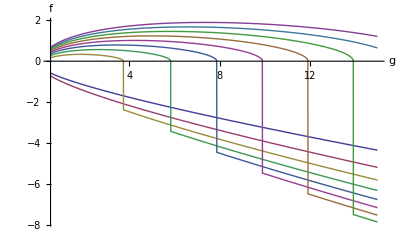

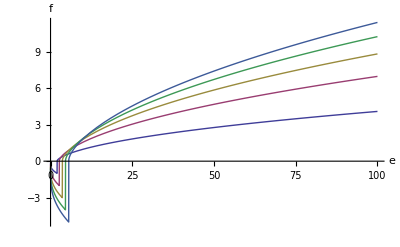

```mathematica
freq[g_, e_]:=(√(-1+(-2+2 e-g) g))/(π+2 ArcTan[(1+g)/(√(-1+(-2+2 e-g) g))]);
Plot[Evaluate[freq[g,e]/.e->Range[1,10,1]],{g,0.5,15},AxesLabel->{g,f}]
Plot[Evaluate[freq[g,e]/.g->Range[1,10,2]],{e,0,100},AxesLabel->{e,f}]
```

### Derivation

```mathematica
Module[{tfull, tapprox, ffull, fapprox},
tfull=Assuming[{ e>1+1/(2g)+g/2,g≥0,e≥0},∫_0^∞ ⅆx/(-x+x^2/2+g(e-x))];
ffull=1/tfull;Print[ffull];
]
```

(√(-1+(-2+2 e-g) g))/(π+2 ArcTan[(1+g)/(√(-1+(-2+2 e-g) g))])

## Bifurcation

For synapse driving soma, bifurcation occurs at g_bif given by:
g_bif=(e-1)±√(e(e-2)+2 r)
Lower values of g_bif are too close together to be useful (due to the distribution) and hence use the upper values of g_bif=(e-1)+√(e(e-2)+2 r). 
Substituting in the circuit parameters using the relations:
r=(2β)/α(I_c/I_leaksoma)^2
g=k_syng I_gset/I_leaksoma
e=k_synerev I_erev/I_leaksoma
we get,
i_gset=1/k_syng(k_synerev i_erev-i_leaksoma +√(4 β/α i_c^2+k_synerev i_erev (k_synerev i_erev-2 i_leaksoma)))
and for r=0,
i_gset=1/k_syng(k_synerev i_erev-i_leaksoma +√(k_synerev i_erev (k_synerev i_erev-2 i_leaksoma)))
⇒i_gset=k_synerev/k_syng i_erev-i_leaksoma/k_syng +√(k_synerev/k_syng i_erev (k_synerev/k_syng i_erev-2 i_leaksoma/k_syng))
(⇒i_gset=C_1 i_ierev-C_2 i_leaksoma+√(C_1 i_erev (C_1 i_erev-2 C_2 i_leaksoma)))
Thus, the different forms of bifurcation point are given from the above expression as:
i_gset=-i_leaksoma/k_syng+(i_erev k_synerev)/k_syng+√(i_erev k_synerev/k_syng (i_erev k_synerev/k_syng-2 1/k_syng i_leaksoma))⇒i_gset=f(1/k_syng i_leaksoma, k_synerev/k_syng i_erev)
i_erev=(i_leaksoma+i_gset k_syng)^2/(2 i_gset k_synerev k_syng)=1/k_synerev i_leaksoma+1/k_synerev^2 i_leaksoma^2 k_synerev/(2 k_syng)1/i_gset+k_syng/(2 k_synerev)i_gset⇒i_erev=f(1/k_synerev i_leaksoma,k_syng/k_synerev i_gset)
i_leaksoma=√(2 k_synerev k_syng)√(i_erev i_gset) -i_gset k_syng⇒√2 √(k_synerev i_erev)√(k_syng i_gset)-k_syng i_gset⇒i_leaksoma=f(k_synerev i_erev,k_syng i_gset)

```mathematica
Expand[(Subscript[i, gset]+Subscript[i, leaksoma]/Subscript[k, syng]-(Subscript[i, erev] Subscript[k, synerev])/Subscript[k, syng])^2-Subscript[i, erev] Subscript[k, synerev]/Subscript[k, syng] (Subscript[i, erev] Subscript[k, synerev]/Subscript[k, syng]-2 1/Subscript[k, syng] Subscript[i, leaksoma])/.{Subscript[i, leaksoma]->xlist,Subscript[i, gset]-> ylist, Subscript[i, erev]-> c2 Subscript[k, syng]/Subscript[k, synerev]}/.Subscript[k, syng]->1/c1]
```

c1^2 xlist^2-2 c2 ylist+2 c1 xlist ylist+ylist^2

### Derivation

#### Approximate

```mathematica
df[r_,g_,e_,τ_]:=(-x+x^2/2+r+g (e-x))/τ;
dfapprox[r_,g_,e_,τ_]:=(x^2/2+r+g (e-x))/τ;
```

```mathematica
Module[{tfull, tapprox, ffull, fapprox},
tapprox=Assuming[r>  -2 e g +(-1-g )^2,∫_0^∞ ⅆx/dfapprox[0,g,e,τ]];
fapprox=1/tapprox;Print[fapprox];
]
```

ConditionalExpression[1/(2 τ (1/2 √(1/(2 e g-g^2)) π+ArcTan[(√g)/(√(2 e-g))]/(√(2 e-g) √g))),g+Re[√(g (-2 e+g))]≤0||√(g (-2 e+g))∉Reals]

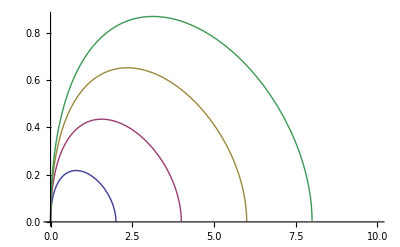

```mathematica
Plot[Evaluate[1/(2 τ (1/2 √(1/(2 e g-g^2)) π+ArcTan[(√g)/(√(2 e-g))]/(√(2 e-g) √g)))/.{τ->1,e->Range[1,4]}],{g,0,10}]
```

```mathematica
Module[{tfull, tapprox, ffull, fapprox},
tapprox=Assuming[r>  -2 e g +(-1-g )^2,∫_0^∞ ⅆx/dfapprox[r,g,e,τ]];
fapprox=1/tapprox;Print[fapprox];
]
```

ConditionalExpression[1/(2 τ (1/2 π √(1/(2 e g-g^2+2 r))+ArcTan[g/(√(2 e g-g^2+2 r))]/(√(2 e g-g^2+2 r)))),g+Re[√(-2 e g+g^2-2 r)]≤0||√(-2 e g+g^2-2 r)∉Reals]

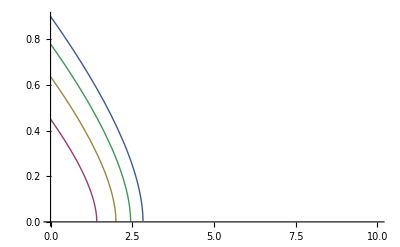

```mathematica
Plot[Evaluate[1/(2 τ (1/2 π √(1/(2 e g-g^2+2 r))+ArcTan[g/(√(2 e g-g^2+2 r))]/(√(2 e g-g^2+2 r))))/.{τ->1,e->0,r->Range[0,4]}],{g,0,10}]
```

#### Exact

```mathematica
Module[{tfull, tapprox, ffull, fapprox},tfull=Assuming[r>  -2 e g +(-1-g )^2,∫_0^∞ ⅆx/df[0,g,e,τ]];
ffull=1/tfull;Print[ffull];
]
```

ConditionalExpression[1/(2 τ (1/2 √(1/(-1+(-2+2 e-g) g)) π+ArcTan[(1+g)/(√(-1+(-2+2 e-g) g))]/(√(-1+(-2+2 e-g) g)))),(1+g≤Re[√(1+2 g-2 e g+g^2)]&&1+g+Re[√(1+2 g-2 e g+g^2)]≤0)||√(1+2 g-2 e g+g^2)∉Reals]

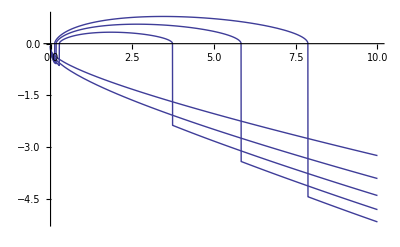

```mathematica
Plot[Re[1/(2 τ (1/2 √(1/(-1+(-2+2 e-g) g)) π+ArcTan[(1+g)/(√(-1+(-2+2 e-g) g))]/(√(-1+(-2+2 e-g) g))))]/.{τ->1,e->Range[1,5]},{g,0,10}]
```

```mathematica
Module[{tfull, tapprox, ffull, fapprox},tfull=Assuming[r>  -2 e g +(-1-g )^2,∫_0^∞ ⅆx/df[r,g,e,τ]];
ffull=1/tfull;Print[ffull];
]
```

ConditionalExpression[1/(2 τ (1/2 π √(1/(-1+(-2+2 e-g) g+2 r))+ArcTan[(1+g)/(√(-1+(-2+2 e-g) g+2 r))]/(√(-1+(-2+2 e-g) g+2 r)))),(1+g≤Re[√(1+2 g-2 e g+g^2-2 r)]&&1+g+Re[√(1+2 g-2 e g+g^2-2 r)]≤0)||√(1+2 g-2 e g+g^2-2 r)∉Reals]

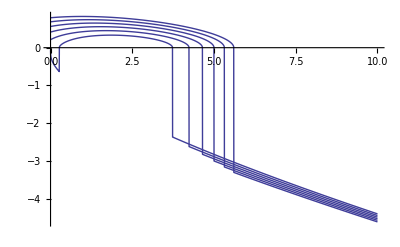

```mathematica
Plot[Re[1/(2 τ (1/2 π √(1/(-1+(-2+2 e-g) g+2 r))+ArcTan[(1+g)/(√(-1+(-2+2 e-g) g+2 r))]/(√(-1+(-2+2 e-g) g+2 r))))]/.{τ->1,e->3,r->Range[0,5]},{g,0,10}]
```

(1+g (2-2 e+g)-2 r)/τ^2

(4 (-2 e+e^2+2 r))/τ^4

{-1+e-√((-2+e) e),-1+e+√((-2+e) e)}

{-1+e-√(-2 e+e^2+2 r),-1+e+√(-2 e+e^2+2 r)}

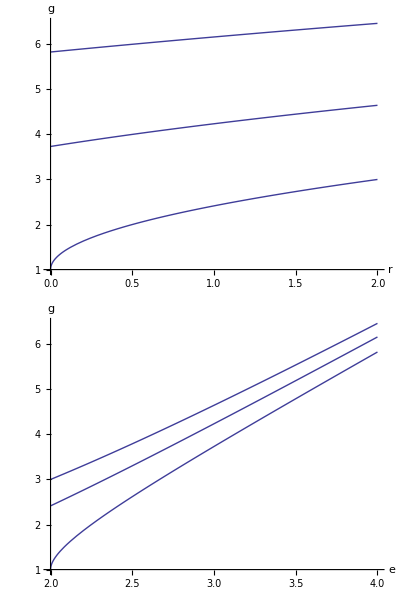

```mathematica
Module[{dfexp, a, b, c,gexp,ag,bg,cg,gdisc, erange, grange},
dfexp=df[r,g,e,τ];
a=Coefficient[dfexp, x,2];
b=Coefficient[dfexp, x,1];
c=Coefficient[dfexp, x,0];
Print[FullSimplify[Expand[b^2-4a c,r]]];
gexp=b^2-4a c;
ag=Coefficient[gexp, g,2];
bg=Coefficient[gexp, g,1];
cg=Coefficient[gexp, g,0];
gdisc=Assuming[τ>0,Simplify[(bg^2-4ag cg)]];Print[gdisc];
(*for r=0*)
gbifnoinp=Simplify[Solve[Evaluate[(b^2-4 a c)/.r->0]==0,g,Reals]];
gbifnoinp=Assuming[e>2,Simplify[g/.gbifnoinp]];Print[gbifnoinp];

(*for r≠0*)
gbif=g/.Assuming[{r≥0,e>2},Simplify[Solve[b^2-4 a c==0,g,Reals]]];
Print[gbif];
Column[{Plot[Table[gbif[[2]],{e, 2, 4}],{r, 0, 2},AxesLabel->{r,g}],
Plot[Table[gbif[[2]],{r, 0, 2}],{e, 2, 4},AxesLabel->{e,g}]},ItemSize->{Automatic,Automatic}]

(*bif=Simplify[Solve[b^2-4 a c==0, g]]; Print[bif];*)
]
```

```mathematica
Module[{g,e,r,gbifplus,gckt,eckt,rckt},
gbifplus=-1+e+√(-2 e+e^2+2 r);
gckt=(Subscript[k, syng] Subscript[i, gset])/Subscript[i, leaksoma];
eckt=(Subscript[k, synerev] Subscript[i, erev])/Subscript[i, leaksoma];
rckt=2 βα (Subscript[i, c]/Subscript[i, leaksoma])^2;
gcomplex=Assuming[{αβ>0,Subscript[i, c]≥0},Simplify[Subscript[i, gset]/.Solve[gckt==gbifplus/.{e->eckt,r->rckt},Subscript[i, gset]]]][[1]];Print[gcomplex];
greal=Assuming[{αβ>0,Subscript[i, c]≥0},Simplify[Subscript[i, gset]/.Solve[gckt==gbifplus/.{e->eckt,r->rckt},Subscript[i, gset],Reals]]][[1]];Print[greal];
]
```

1/k_syng(i_erev k_synerev+i_leaksoma (-1+√((4 βα i_c^2+i_erev k_synerev (-2 i_leaksoma+i_erev k_synerev))/i_leaksoma^2)))

ConditionalExpression[1/k_syng(i_erev k_synerev+i_leaksoma (-1+√((4 βα i_c^2+i_erev k_synerev (-2 i_leaksoma+i_erev k_synerev))/i_leaksoma^2))),i_c>0&&2 i_erev i_leaksoma k_synerev<4 βα i_c^2+i_erev^2 k_synerev^2]

```mathematica
(*Expression for bifurcation with no input*)
Module[{g,e,gbifplus,gckt,eckt,rckt},
gbifplus=-1+e+√(-2 e+e^2);
gckt=(Subscript[k, syng] Subscript[i, gset])/Subscript[i, leaksoma];
eckt=(Subscript[k, synerev] Subscript[i, erev])/Subscript[i, leaksoma];
gcomplex=Assuming[{Subscript[i, leaksoma]>0,Subscript[i, erev]>0,Subscript[i, gset]>0},Simplify[Subscript[i, gset]/.Solve[gckt==gbifplus/.{e->eckt},Subscript[i, gset]]]][[1]];

gcomplex=Assuming[{Subscript[C, 1]>0,Subscript[C, 2]>0},Simplify[gcomplex/.{Subscript[k, syng]->1/Subscript[C, 2],Subscript[k, synerev]->Subscript[C, 1]/Subscript[C, 2]}]];
Print[Collect[gcomplex,{Subscript[i, erev],Subscript[i, leaksoma]}]];
ecomplex=Solve[Subscript[i, gset]==gcomplex,Subscript[i, erev]];
Print[ecomplex[[1]]];
lcomplex=Solve[Subscript[i, gset]==gcomplex,Subscript[i, leaksoma]];
Print[lcomplex[[2]]];
(*
greal=Assuming[{},Simplify[Subscript[i, gset]/.Solve[gckt==gbifplus/.{e->eckt},Subscript[i, gset],Reals]]][[1]];Print[greal];
*)
Print[]; Print[];
Print[{Subscript[C, 1],Subscript[C, 2],Subscript[C, 1]^2,2 Subscript[C, 1] Subscript[C, 2]}/.Subscript[C, 1]->Subscript[k, synerev] Subscript[C, 2]/.Subscript[C, 2]->1/Subscript[k, syng]];
Print[{1/(2 Subscript[C, 1]),Subscript[C, 2]/Subscript[C, 1],Subscript[C, 2]^2/(2 Subscript[C, 1])}/.Subscript[C, 1]->Subscript[k, synerev] Subscript[C, 2]/.Subscript[C, 2]->1/Subscript[k, syng]];
Print[{√(2 Subscript[C, 1])/Subscript[C, 2],1/Subscript[C, 2]}/.Subscript[C, 1]->Subscript[k, synerev] Subscript[C, 2]/.Subscript[C, 2]->1/Subscript[k, syng]];
];
```

C_1 i_erev-C_2 i_leaksoma+√(C_1 i_erev (C_1 i_erev-2 C_2 i_leaksoma))

{i_erev→(i_gset+C_2 i_leaksoma)^2/(2 C_1 i_gset)}

{i_leaksoma→(√2 √C_1 √i_erev √i_gset-i_gset)/C_2}

{k_synerev/k_syng,1/k_syng,k_synerev^2/k_syng^2,(2 k_synerev)/k_syng^2}

{k_syng/(2 k_synerev),1/k_synerev,1/(2 k_synerev k_syng)}

{√2 √(k_synerev/k_syng) k_syng,k_syng}

```mathematica
(*Expression for bifurcation with no input*)
Module[{g,e,gbifplus,gckt,eckt,rckt},
gbifplus=-1+e+√(-2 e+e^2);
gckt=(Subscript[k, syng] Subscript[i, gset])/Subscript[i, leaksoma];
eckt=(Subscript[k, synerev] Subscript[i, erev])/Subscript[i, leaksoma];
gcomplex=Assuming[{Subscript[i, leaksoma]>0,Subscript[i, erev]>0,Subscript[i, gset]>0},Simplify[Subscript[i, gset]/.Solve[gckt==gbifplus/.{e->eckt},Subscript[i, gset]]]][[1]];

gcomplex=Assuming[{Subscript[k, syng]>0,Subscript[k, synerev]>0},Simplify[gcomplex]];
Print[Collect[gcomplex,{Subscript[i, erev],Subscript[i, leaksoma]}]];
ecomplex=Solve[Subscript[i, gset]==gcomplex,Subscript[i, erev]];
Print[{ecomplex[[1]],Expand[ecomplex[[1]]]}];
lcomplex=Solve[Subscript[i, gset]==gcomplex,Subscript[i, leaksoma]];
Print[lcomplex[[2]]];
(*
greal=Assuming[{},Simplify[Subscript[i, gset]/.Solve[gckt==gbifplus/.{e->eckt},Subscript[i, gset],Reals]]][[1]];Print[greal];
*)
];
```

-i_leaksoma/k_syng+(i_erev k_synerev)/k_syng+(√(i_erev k_synerev (-2 i_leaksoma+i_erev k_synerev)))/k_syng

{{i_erev→(i_leaksoma+i_gset k_syng)^2/(2 i_gset k_synerev k_syng)},{i_erev→i_leaksoma/k_synerev+i_leaksoma^2/(2 i_gset k_synerev k_syng)+(i_gset k_syng)/(2 k_synerev)}}

{i_leaksoma→√2 √i_erev √i_gset √k_synerev √k_syng-i_gset k_syng}

### Bifurcation Trends

```mathematica
igsetbif[c1_,ierev_,c2_,ileaksoma_]:=c1 ierev-c2 ileaksoma+√(c1 ierev(c1 ierev-2 c2 ileaksoma));
ierevbif[c1_, igset_, c2_, ileaksoma_]:=c1/2 igset+c2 ileaksoma+c2^2 ileaksoma^2 1/(2c1)1/igset;
ileaksomabif[c1_, ierev_, c2_, igset_]:=√(2 c1 ierev c2 igset)-c2 igset;

Needs["PlotLegends`"];
SetOptions[Plot,PlotStyle->Thick];

pga=Plot[Evaluate[igsetbif[c1, ierev, c2, ileaksoma]/.{c1->1, c2->1,ierev->Range[0.5, 2.5, 0.5]}], {ileaksoma, 0.01, 1}, AxesLabel->{"I_leaksoma","I_gset"},PlotLabel->"bifurcation I_gset for various I_erev",PlotLegend-> Range[0.5, 2.5, 0.5],LegendShadow-> None];
pgb=Plot[Evaluate[igsetbif[c1, ierev, c2, ileaksoma]/.{c1->1, c2->1,ileaksoma->Range[0.01, 1, 0.25]}], {ierev, 0.5, 2.5}, AxesLabel->{"I_erev","I_gset"},PlotLabel->"bifurcation I_gset for various I_leaksoma",PlotLegend->Range[0.01, 1, 0.25],LegendShadow-> None ];

pea=Plot[Evaluate[ierevbif[c1, igset, c2, ileaksoma]/.{c1->1, c2->1,igset->Range[1, 5,1]}], {ileaksoma, 0.01, 1}, AxesLabel->{"I_leaksoma","I_erev"},PlotLabel->"bifurcation I_erev for various I_gset",PlotLegend-> Range[1, 5,1],LegendShadow-> None];
peb=Plot[Evaluate[ierevbif[c1, igset, c2, ileaksoma]/.{c1->1, c2->1,ileaksoma->Range[0.01, 1, 0.25]}], {igset, 0, 5}, AxesLabel->{"I_gset","I_erev"},PlotLabel->"bifurcation I_erev for various I_leaksoma",PlotLegend->Range[0.01, 1, 0.25],LegendShadow-> None ];

pla=Plot[Evaluate[ileaksomabif[c1, ierev, c2, igset]/.{c1->1, c2->1,ierev->Range[0.5, 2.5, 0.5]}], {igset,0,5}, AxesLabel->{"I_gset","I_leaksoma"},PlotLabel->"bifurcation I_leaksoma for various I_erev",PlotLegend-> Range[0.5, 2.5, 0.5],LegendShadow-> None];
plb=Plot[Evaluate[ileaksomabif[c1, ierev, c2, igset]/.{c1->1, c2->1,igset->Range[1, 5,1]}, {ierev, 0.5, 2.5}], AxesLabel->{"I_erev","I_leaksoma"},PlotLabel->"bifurcation I_leaksoma for various I_gset",PlotLegend-> Range[1, 5,1],LegendShadow-> None];
GraphicsGrid[{{pga, pgb}, {pea, peb}, {pla, plb}}, ImageSize->500,AspectRatio->1,Frame->All]
```

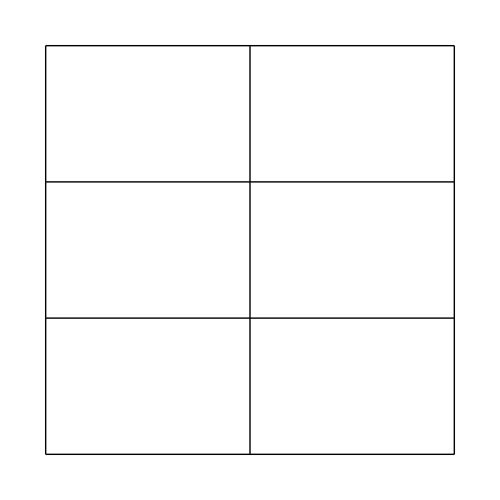

### Testing

```mathematica
igsetbif[c1_,ierev_,c2_,ileaksoma_]:=c1 ierev-c2 ileaksoma+√(c1 ierev(c1 ierev-2 c2 ileaksoma));
ierevbif[c1_, igset_, c2_, ileaksoma_]:=c1/2 igset+c2 ileaksoma+c2^2 ileaksoma^2 1/(2c1)1/igset;
ileaksomabif[c1_, ierev_, c2_, igset_]:=√(2 c1 ierev c2 igset)-c2 igset;

Needs["PlotLegends`"];
SetOptions[Plot,PlotStyle->Thick];
```

```mathematica
Plot[Evaluate[igsetbif[c1, ierev, c2, ileaksoma]/.{c1->1, c2->1,ierev->Range[0.5, 2.5, 0.5]}], {ileaksoma, 0.01, 1}, AxesLabel->{Subscript[i, leaksoma],Subscript[i, gset]},PlotLabel->"bifurcation i_gset for various i_erev",PlotLegend-> Range[0.5, 2.5, 0.5],LegendShadow-> None]
Plot[Evaluate[igsetbif[c1, ierev, c2, ileaksoma]/.{c1->1, c2->1,ileaksoma->Range[0.01, 1, 0.25]}], {ierev, 0.5, 2.5}, AxesLabel->{Subscript[i, erev],Subscript[i, gset]},PlotLabel->"bifurcation i_gset for various i_leaksoma",PlotLegend->Range[0.01, 1, 0.25],LegendShadow-> None ]
```

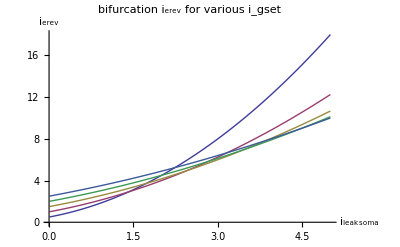

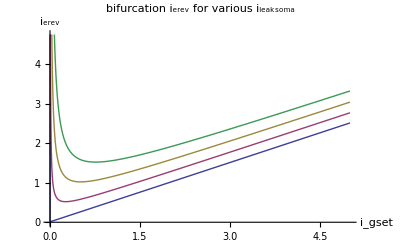

```mathematica
Plot[Evaluate[ierevbif[c1, igset, c2, ileaksoma]/.{c1->1, c2->1,igset->Range[1, 5,1]}], {ileaksoma, 0.01, 5}, AxesLabel->{Subscript[i, leaksoma],Subscript[i, erev]},PlotLabel->"bifurcation i_erev for various i_gset",PlotLegend-> Range[1, 5,1],LegendShadow-> None]
Plot[Evaluate[ierevbif[c1, igset, c2, ileaksoma]/.{c1->1, c2->1,ileaksoma->Range[0.01, 1, 0.25]}], {igset, 0, 5}, AxesLabel->{Subscript[i, gset],Subscript[i, erev]},PlotLabel->"bifurcation i_erev for various i_leaksoma",PlotLegend->Range[0.01, 1, 0.25],LegendShadow-> None ]
```

```mathematica
Plot[Evaluate[ileaksomabif[c1, ierev, c2, igset]/.{c1->1, c2->1,ierev->Range[0.5, 2.5, 0.5]}], {igset,0,5}, AxesLabel->{Subscript[i, gset],Subscript[i, leaksoma]},PlotLabel->"bifurcation i_leaksoma for various i_erev",PlotLegend-> Range[0.5, 2.5, 0.5],LegendShadow-> None]
Plot[Evaluate[ileaksomabif[c1, ierev, c2, igset]/.{c1->1, c2->1,igset->Range[1, 5,1]}, {ierev, 0.5, 2.5}], AxesLabel->{Subscript[i, erev],Subscript[i, leaksoma]},PlotLabel->"bifurcation i_leaksoma for various i_gset",PlotLegend-> Range[1, 5,1],LegendShadow-> None]
```

## Dimensionless Dendrite with Synapse

Quadratic LIF Neuron without synapse
τ ḋ=-d+d_ss
Quadratic LIF Neuron with synapse
τ ḋ=-d+d_ss+g_d(e_d-d)

## Dimensional Form

We have, for the conductance:
K_1 I_leaklpf I_gset=I_gsyn I_syn
K_2 I_leaklpf=I_lsyn
C OverDot[V_syn]=I_lsyn-I_gsyn=K_2 I_leaklpf-K_1(I_leaklpf I_gset)/I_syn
(C V_T)/κ OverDot[I_syn]/-I_syn=K_2 I_leaklpf-K_1(I_leaklpf I_gset)/I_syn
K_3(C V_T)/(κ I_leaklpf)OverDot[I_syn]=-I_syn+γ_1 I_gset
τ_psyn/I_leaklpf OverDot[I_syn]=-I_syn+γ_1 I_gset
We have, for the reversal potential:
K_1/K_d I_syn I_gerev=I_synsink I_d
K_2 I_erev=I_gerev
Current flowing into dendrite:
K_3 I_syn-I_synsink=K_3 I_syn-K_4/K_d (I_syn I_erev)/I_d=I_syn/I_d(K_3 I_d-K_4/K_d I_erev)
Full Equation for the dendrite is then:
(C V_T)/κ(-1/I_d)(İ)_d=w_leakdend I_leakdend-β'_d((I^2)_backdend)/I_d+I_syn/I_d(K_3 I_d-K_4/K_d I_erev)
τ_p/I_leakdend(İ)_d=-I_d+β_d((I^2)_backdend)/I_leakdend+I_syn/I_leakdend(K'_4/K_d I_erev-K'_3 I_d)
τ_p/I_leakdend(i̇)_d=-i_d+β_d((I^2)_backdend)/I_leakdend+γ_2 I_syn/I_leakdend(γ_3/K_d I_erev-i_d)
using I_d= i_d.
For steady state I_syn=γ_1 I_gset (using long I_leakpe with short input spikes and short enough τ_syn), we get:
τ_p/I_leakdend(i̇)_d=-i_d+β_d((I^2)_backdend)/I_leakdend+γ_4 I_gset/I_leakdend(γ_3/K_d I_erev-i_d)
Normalizing with i_mth=α/(2β)i_leaksoma^2/ϵ_c, d=(2β)/α ϵ_c/i_leaksoma^2 i_d:
τ_p/I_leakdend ḋ=-d+2/p_qua ϵ_c/i_leaksoma^2 β_d((I^2)_backdend)/I_leakdend+γ_4 I_gset/I_leakdend(ϵ_c/i_leaksoma 2/p_qua γ_3/K_d I_erev/i_leaksoma-d)
τ_p/I_leaksoma ḋ=-d+d_ss+γ_4/k_syng i_leaksoma/I_leakdend g(ϵ_c/i_leaksoma 2/p_qua γ_3/k_synerev e/K_d-d)     [note: k_syng→γ_4,k_synerev→(2 γ_3)/p_qua]
τ_p/I_leaksoma ḋ=-d+d_ss+i_leaksoma/I_leakdend g(ϵ_c/i_leaksoma e/K_d-d)
Hence:
d_ss=
g_d=
e_d=
(Note: p_qua=α/β)

## Circuit derivation

Assuming M_R2is in saturation:
I_gsyn=I_0 e^(-(κ(V_gsat-V_R))/V_T)
I_gsyn=I_0 e^(-(κ(V_C-V_R))/V_T)